/homes/ht/Desktop/workspace/dna_live/thesis_results/dna_large_etab/ksr150/N49/results/Intact

{{L:,60.2},{m:,150},{N:,49},{kappa:,0.1},{sigma:,0.000666},{kappa_sigma_r:,150.15},{Delta:,0.2},{Extension Minimum:,0},{Extension Maximum:,70},{e0:,0.0222},{Beta:,38.6817}}

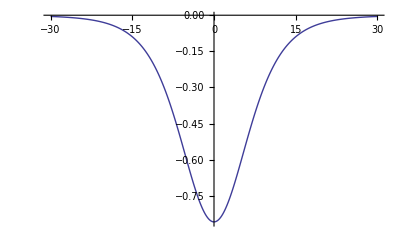

Backbone spring constant κ:

0.1

Base-pair spring constant σ(ϵ = 0.0222):

0.000666

κ/σ ratio:

150.15

```mathematica
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["../Parameters"]
Potential=Import["../Potential_Data.out","Table"];
ListLinePlot[Potential,PlotStyle->{Thick},AxesOrigin->{0,0},PlotRange->All]

IntactPF=Import["PartitionFunction_0_0.out","Table"];
IntactFE=Import["FreeEnergy_0_0.out","Table"];
IntactdFE=Import["dFreeEnergy_0_0.out","Table"];

IntactZNJη=Import["znj_eta.out","Table"];
IntactZNJξ=Import["znj_xi.out","Table"];

IntactMXDη=Import["MeanAxialDisp_eta.out","Table"];
IntactMXDξ=Import["MeanAxialDisp_xi.out","Table"];

AverageX= Import["Average_X.out","Table"];
AverageY= Import["Average_Y.out","Table"];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

T=300 SI[Kelvin];
n=Parameters[[3,2]];
Print["Backbone spring constant κ:"]
κ=Parameters[[4,2]]
Print["Base-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[5,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[6,2]]
Δ=Parameters[[7,2]];

umin=Parameters[[8,2]];
umax=Parameters[[9,2]];

ϵ=Parameters[[10,2]];(*eV*)
β=Parameters[[11,2]];(*eV^-1*) 

Subscript[η, B]=2.0;
ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1 ;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f(κ/(4β))^(1/2)) ToNewton;
ToDimension[η_]:=η((κ β)/4)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]] (*Å*)
```

2.

2.0338

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

2.17016

20.3656

## Numerical Results

### Partition Function & Free Energy

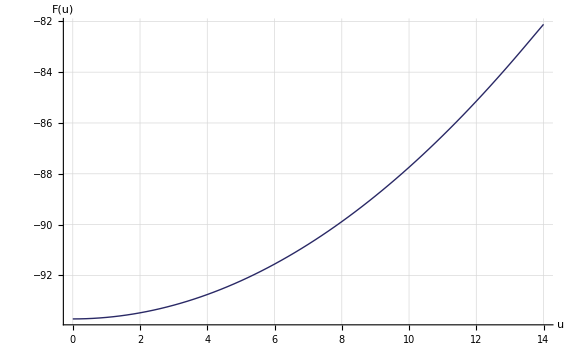
{-Graphics-,-Graphics-}

```mathematica
pIntactPF=ListLinePlot[
IntactPF,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["Z(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
];

pIntactFE=ListLinePlot[
IntactFE,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["F(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
];

{pIntactPF,pIntactFE}
```

### Mean Axial Displacement of ξ and η

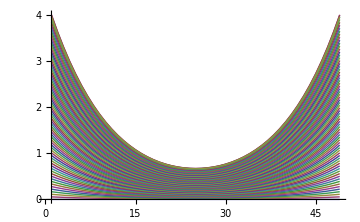
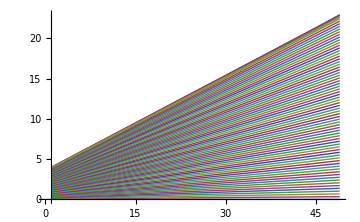

1.98434

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0557699 | 0.0503385 | 0.045436 | 0.0410163 | 0.0370367 | 0.0334576 | 0.0302427 | 0.0273588 | 0.0247758 | 0.0224663 | 0.0204057 | 0.0185717 | 0.0169444 | 0.015506 | 0.0142408 | 0.0131349 | 0.012176 | 0.0113535 | 0.0106583 | 0.0100827 | 0.00962026 | 0.00926582 | 0.00901543 | 0.00886631 | 0.00881678 | 0.00886631 | 0.00901543 | 0.00926582 | 0.00962026 | 0.0100827 | 0.0106583 | 0.0113535 | 0.012176 | 0.0131349 | 0.0142408 | 0.015506 | 0.0169444 | 0.0185717 | 0.0204057 | 0.0224663 | 0.0247758 | 0.0273588 | 0.0302427 | 0.0334576 | 0.0370367 | 0.0410163 | 0.045436 | 0.0503385 | 0.0557699
0.111544 | 0.100681 | 0.0908764 | 0.0820369 | 0.0740775 | 0.066919 | 0.0604889 | 0.0547209 | 0.0495547 | 0.0449355 | 0.040814 | 0.0371458 | 0.033891 | 0.0310141 | 0.0284836 | 0.0262716 | 0.0243537 | 0.0227086 | 0.0213182 | 0.0201669 | 0.0192419 | 0.018533 | 0.0180322 | 0.0177339 | 0.0176348 | 0.0177339 | 0.0180322 | 0.018533 | 0.0192419 | 0.0201669 | 0.0213182 | 0.0227086 | 0.0243537 | 0.0262716 | 0.0284836 | 0.0310141 | 0.033891 | 0.0371458 | 0.040814 | 0.0449355 | 0.0495547 | 0.0547209 | 0.0604889 | 0.066919 | 0.0740775 | 0.0820369 | 0.0908764 | 0.100681 | 0.111544
0.167327 | 0.151033 | 0.136326 | 0.123066 | 0.111126 | 0.100388 | 0.0907423 | 0.0820897 | 0.0743398 | 0.0674104 | 0.0612277 | 0.0557248 | 0.0508422 | 0.0465264 | 0.0427303 | 0.039412 | 0.0365348 | 0.0340669 | 0.031981 | 0.0302539 | 0.0288663 | 0.0278028 | 0.0270515 | 0.026604 | 0.0264554 | 0.026604 | 0.0270515 | 0.0278028 | 0.0288663 | 0.0302539 | 0.031981 | 0.0340669 | 0.0365348 | 0.039412 | 0.0427303 | 0.0465264 | 0.0508422 | 0.0557248 | 0.0612277 | 0.0674104 | 0.0743398 | 0.0820897 | 0.0907423 | 0.100388 | 0.111126 | 0.123066 | 0.136326 | 0.151033 | 0.167327
0.223124 | 0.201399 | 0.181788 | 0.164108 | 0.148187 | 0.133868 | 0.121006 | 0.109468 | 0.0991341 | 0.089894 | 0.0816493 | 0.0743112 | 0.0678002 | 0.0620451 | 0.0569828 | 0.0525577 | 0.048721 | 0.04543 | 0.0426484 | 0.0403452 | 0.0384948 | 0.0370765 | 0.0360746 | 0.035478 | 0.0352798 | 0.035478 | 0.0360746 | 0.0370765 | 0.0384948 | 0.0403452 | 0.0426484 | 0.04543 | 0.048721 | 0.0525577 | 0.0569828 | 0.0620451 | 0.0678002 | 0.0743112 | 0.0816493 | 0.089894 | 0.0991341 | 0.109468 | 0.121006 | 0.133868 | 0.148187 | 0.164108 | 0.181788 | 0.201399 | 0.223124
0.278938 | 0.251782 | 0.227268 | 0.205167 | 0.185264 | 0.167364 | 0.151285 | 0.136861 | 0.123941 | 0.112389 | 0.102082 | 0.0929075 | 0.0847672 | 0.0775721 | 0.0712432 | 0.0657108 | 0.0609139 | 0.0567995 | 0.0533218 | 0.0504422 | 0.0481287 | 0.0463556 | 0.045103 | 0.044357 | 0.0441092 | 0.044357 | 0.045103 | 0.0463556 | 0.0481287 | 0.0504422 | 0.0533218 | 0.0567995 | 0.0609139 | 0.0657108 | 0.0712432 | 0.0775721 | 0.0847672 | 0.0929075 | 0.102082 | 0.112389 | 0.123941 | 0.136861 | 0.151285 | 0.167364 | 0.185264 | 0.205167 | 0.227268 | 0.251782 | 0.278938
0.334775 | 0.302187 | 0.27277 | 0.246247 | 0.222362 | 0.200879 | 0.181581 | 0.16427 | 0.148763 | 0.134898 | 0.122527 | 0.111516 | 0.101746 | 0.0931097 | 0.0855133 | 0.0788729 | 0.0731154 | 0.0681769 | 0.0640027 | 0.0605464 | 0.0577696 | 0.0556413 | 0.0541378 | 0.0532424 | 0.052945 | 0.0532424 | 0.0541378 | 0.0556413 | 0.0577696 | 0.0605464 | 0.0640027 | 0.0681769 | 0.0731154 | 0.0788729 | 0.0855133 | 0.0931097 | 0.101746 | 0.111516 | 0.122527 | 0.134898 | 0.148763 | 0.16427 | 0.181581 | 0.200879 | 0.222362 | 0.246247 | 0.27277 | 0.302187 | 0.334775
0.390638 | 0.35262 | 0.318298 | 0.287352 | 0.259484 | 0.234417 | 0.211899 | 0.191698 | 0.173604 | 0.157425 | 0.142989 | 0.130139 | 0.118738 | 0.10866 | 0.0997951 | 0.092046 | 0.0853271 | 0.0795639 | 0.0746927 | 0.0706592 | 0.0674187 | 0.064935 | 0.0631804 | 0.0621355 | 0.0617885 | 0.0621355 | 0.0631804 | 0.064935 | 0.0674187 | 0.0706592 | 0.0746927 | 0.0795639 | 0.0853271 | 0.092046 | 0.0997951 | 0.10866 | 0.118738 | 0.130139 | 0.142989 | 0.157425 | 0.173604 | 0.191698 | 0.211899 | 0.234417 | 0.259484 | 0.287352 | 0.318298 | 0.35262 | 0.390638
0.446532 | 0.403084 | 0.363857 | 0.328487 | 0.296634 | 0.267982 | 0.242242 | 0.219151 | 0.198467 | 0.179972 | 0.163469 | 0.14878 | 0.135746 | 0.124225 | 0.114091 | 0.105232 | 0.0975507 | 0.0909621 | 0.0853932 | 0.0807821 | 0.0770774 | 0.074238 | 0.0722321 | 0.0710375 | 0.0706408 | 0.0710375 | 0.0722321 | 0.074238 | 0.0770774 | 0.0807821 | 0.0853932 | 0.0909621 | 0.0975507 | 0.105232 | 0.114091 | 0.124225 | 0.135746 | 0.14878 | 0.163469 | 0.179972 | 0.198467 | 0.219151 | 0.242242 | 0.267982 | 0.296634 | 0.328487 | 0.363857 | 0.403084 | 0.446532
0.502462 | 0.453584 | 0.409452 | 0.369657 | 0.333816 | 0.301577 | 0.272614 | 0.24663 | 0.223355 | 0.202542 | 0.18397 | 0.16744 | 0.152772 | 0.139807 | 0.128402 | 0.118432 | 0.109788 | 0.102373 | 0.0961059 | 0.0909165 | 0.0867472 | 0.0835516 | 0.0812942 | 0.0799498 | 0.0795033 | 0.0799498 | 0.0812942 | 0.0835516 | 0.0867472 | 0.0909165 | 0.0961059 | 0.102373 | 0.109788 | 0.118432 | 0.128402 | 0.139807 | 0.152772 | 0.16744 | 0.18397 | 0.202542 | 0.223355 | 0.24663 | 0.272614 | 0.301577 | 0.333816 | 0.369657 | 0.409452 | 0.453584 | 0.502462
0.558433 | 0.504124 | 0.455086 | 0.410865 | 0.371036 | 0.335207 | 0.303018 | 0.27414 | 0.24827 | 0.225138 | 0.204496 | 0.186123 | 0.169819 | 0.155408 | 0.142731 | 0.131649 | 0.122041 | 0.113799 | 0.106832 | 0.101064 | 0.0964294 | 0.0928773 | 0.0903681 | 0.0888736 | 0.0883773 | 0.0888736 | 0.0903681 | 0.0928773 | 0.0964294 | 0.101064 | 0.106832 | 0.113799 | 0.122041 | 0.131649 | 0.142731 | 0.155408 | 0.169819 | 0.186123 | 0.204496 | 0.225138 | 0.24827 | 0.27414 | 0.303018 | 0.335207 | 0.371036 | 0.410865 | 0.455086 | 0.504124 | 0.558433
0.614447 | 0.554709 | 0.500765 | 0.452115 | 0.408296 | 0.368875 | 0.333459 | 0.301683 | 0.273217 | 0.247763 | 0.225048 | 0.20483 | 0.186889 | 0.17103 | 0.157079 | 0.144884 | 0.13431 | 0.12524 | 0.117574 | 0.111226 | 0.106125 | 0.102216 | 0.0994549 | 0.0978103 | 0.0972641 | 0.0978103 | 0.0994549 | 0.102216 | 0.106125 | 0.111226 | 0.117574 | 0.12524 | 0.13431 | 0.144884 | 0.157079 | 0.17103 | 0.186889 | 0.20483 | 0.225048 | 0.247763 | 0.273217 | 0.301683 | 0.333459 | 0.368875 | 0.408296 | 0.452115 | 0.500765 | 0.554709 | 0.614447
0.670511 | 0.605344 | 0.546492 | 0.493413 | 0.445601 | 0.402586 | 0.363939 | 0.329263 | 0.298199 | 0.27042 | 0.24563 | 0.223565 | 0.203984 | 0.186675 | 0.17145 | 0.15814 | 0.146599 | 0.136699 | 0.128332 | 0.121403 | 0.115837 | 0.11157 | 0.108556 | 0.106761 | 0.106165 | 0.106761 | 0.108556 | 0.11157 | 0.115837 | 0.121403 | 0.128332 | 0.136699 | 0.146599 | 0.15814 | 0.17145 | 0.186675 | 0.203984 | 0.223565 | 0.24563 | 0.27042 | 0.298199 | 0.329263 | 0.363939 | 0.402586 | 0.445601 | 0.493413 | 0.546492 | 0.605344 | 0.670511
0.726629 | 0.656032 | 0.592272 | 0.534762 | 0.482954 | 0.436343 | 0.394462 | 0.356883 | 0.323218 | 0.293111 | 0.266244 | 0.242329 | 0.221107 | 0.202346 | 0.185844 | 0.171417 | 0.158908 | 0.148178 | 0.139108 | 0.131598 | 0.125565 | 0.12094 | 0.117673 | 0.115727 | 0.115081 | 0.115727 | 0.117673 | 0.12094 | 0.125565 | 0.131598 | 0.139108 | 0.148178 | 0.158908 | 0.171417 | 0.185844 | 0.202346 | 0.221107 | 0.242329 | 0.266244 | 0.293111 | 0.323218 | 0.356883 | 0.394462 | 0.436343 | 0.482954 | 0.534762 | 0.592272 | 0.656032 | 0.726629
0.782805 | 0.70678 | 0.63811 | 0.576167 | 0.520362 | 0.470151 | 0.425033 | 0.384548 | 0.348278 | 0.315841 | 0.286894 | 0.261126 | 0.238259 | 0.218045 | 0.200264 | 0.184719 | 0.17124 | 0.159678 | 0.149905 | 0.141812 | 0.135311 | 0.130328 | 0.126807 | 0.124711 | 0.124014 | 0.124711 | 0.126807 | 0.130328 | 0.135311 | 0.141812 | 0.149905 | 0.159678 | 0.17124 | 0.184719 | 0.200264 | 0.218045 | 0.238259 | 0.261126 | 0.286894 | 0.315841 | 0.348278 | 0.384548 | 0.425033 | 0.470151 | 0.520362 | 0.576167 | 0.63811 | 0.70678 | 0.782805
0.839044 | 0.757591 | 0.684011 | 0.617632 | 0.557826 | 0.504012 | 0.455654 | 0.41226 | 0.373382 | 0.338611 | 0.307581 | 0.279958 | 0.255444 | 0.233774 | 0.214711 | 0.198046 | 0.183596 | 0.1712 | 0.160723 | 0.152047 | 0.145077 | 0.139734 | 0.13596 | 0.133712 | 0.132965 | 0.133712 | 0.13596 | 0.139734 | 0.145077 | 0.152047 | 0.160723 | 0.1712 | 0.183596 | 0.198046 | 0.214711 | 0.233774 | 0.255444 | 0.279958 | 0.307581 | 0.338611 | 0.373382 | 0.41226 | 0.455654 | 0.504012 | 0.557826 | 0.617632 | 0.684011 | 0.757591 | 0.839044
0.89535 | 0.80847 | 0.729978 | 0.659161 | 0.595352 | 0.537932 | 0.48633 | 0.440023 | 0.398533 | 0.361426 | 0.328308 | 0.298827 | 0.272664 | 0.249535 | 0.229189 | 0.211401 | 0.195978 | 0.182747 | 0.171564 | 0.162303 | 0.154863 | 0.149161 | 0.145132 | 0.142733 | 0.141936 | 0.142733 | 0.145132 | 0.149161 | 0.154863 | 0.162303 | 0.171564 | 0.182747 | 0.195978 | 0.211401 | 0.229189 | 0.249535 | 0.272664 | 0.298827 | 0.328308 | 0.361426 | 0.398533 | 0.440023 | 0.48633 | 0.537932 | 0.595352 | 0.659161 | 0.729978 | 0.80847 | 0.89535
0.951729 | 0.859421 | 0.776017 | 0.70076 | 0.632944 | 0.571915 | 0.517065 | 0.467841 | 0.423735 | 0.384287 | 0.349079 | 0.317737 | 0.289921 | 0.265331 | 0.243698 | 0.224786 | 0.208387 | 0.19432 | 0.182429 | 0.172583 | 0.164672 | 0.158609 | 0.154326 | 0.151775 | 0.150927 | 0.151775 | 0.154326 | 0.158609 | 0.164672 | 0.172583 | 0.182429 | 0.19432 | 0.208387 | 0.224786 | 0.243698 | 0.265331 | 0.289921 | 0.317737 | 0.349079 | 0.384287 | 0.423735 | 0.467841 | 0.517065 | 0.571915 | 0.632944 | 0.70076 | 0.776017 | 0.859421 | 0.951729
1.00818 | 0.91045 | 0.822131 | 0.742432 | 0.670607 | 0.605963 | 0.547862 | 0.495717 | 0.448991 | 0.407198 | 0.369897 | 0.336689 | 0.307217 | 0.281163 | 0.258242 | 0.238203 | 0.220827 | 0.205921 | 0.193321 | 0.182888 | 0.174506 | 0.168081 | 0.163542 | 0.160839 | 0.159941 | 0.160839 | 0.163542 | 0.168081 | 0.174506 | 0.182888 | 0.193321 | 0.205921 | 0.220827 | 0.238203 | 0.258242 | 0.281163 | 0.307217 | 0.336689 | 0.369897 | 0.407198 | 0.448991 | 0.495717 | 0.547862 | 0.605963 | 0.670607 | 0.742432 | 0.822131 | 0.91045 | 1.00818
1.06472 | 0.961561 | 0.868327 | 0.784182 | 0.708344 | 0.640082 | 0.578725 | 0.523654 | 0.474305 | 0.430163 | 0.390764 | 0.355687 | 0.324556 | 0.297034 | 0.272821 | 0.251653 | 0.233298 | 0.217552 | 0.204241 | 0.19322 | 0.184364 | 0.177577 | 0.172782 | 0.169927 | 0.168978 | 0.169927 | 0.172782 | 0.177577 | 0.184364 | 0.19322 | 0.204241 | 0.217552 | 0.233298 | 0.251653 | 0.272821 | 0.297034 | 0.324556 | 0.355687 | 0.390764 | 0.430163 | 0.474305 | 0.523654 | 0.578725 | 0.640082 | 0.708344 | 0.784182 | 0.868327 | 0.961561 | 1.06472
1.12134 | 1.01276 | 0.914608 | 0.826015 | 0.746159 | 0.674276 | 0.609658 | 0.551657 | 0.499679 | 0.453184 | 0.411682 | 0.374733 | 0.341939 | 0.312947 | 0.28744 | 0.26514 | 0.245802 | 0.229213 | 0.215191 | 0.20358 | 0.19425 | 0.1871 | 0.182048 | 0.179039 | 0.17804 | 0.179039 | 0.182048 | 0.1871 | 0.19425 | 0.20358 | 0.215191 | 0.229213 | 0.245802 | 0.26514 | 0.28744 | 0.312947 | 0.341939 | 0.374733 | 0.411682 | 0.453184 | 0.499679 | 0.551657 | 0.609658 | 0.674276 | 0.746159 | 0.826015 | 0.914608 | 1.01276 | 1.12134
1.17806 | 1.06405 | 0.960979 | 0.867936 | 0.784058 | 0.708548 | 0.640665 | 0.579729 | 0.525117 | 0.476264 | 0.432656 | 0.39383 | 0.35937 | 0.328903 | 0.302098 | 0.278664 | 0.258342 | 0.240908 | 0.226172 | 0.213969 | 0.204165 | 0.19665 | 0.191341 | 0.188179 | 0.187129 | 0.188179 | 0.191341 | 0.19665 | 0.204165 | 0.213969 | 0.226172 | 0.240908 | 0.258342 | 0.278664 | 0.302098 | 0.328903 | 0.35937 | 0.39383 | 0.432656 | 0.476264 | 0.525117 | 0.579729 | 0.640665 | 0.708548 | 0.784058 | 0.867936 | 0.960979 | 1.06405 | 1.17806
1.23487 | 1.11543 | 1.00745 | 0.909948 | 0.822045 | 0.742903 | 0.67175 | 0.607873 | 0.550623 | 0.499407 | 0.453688 | 0.412981 | 0.37685 | 0.344905 | 0.3168 | 0.292227 | 0.270918 | 0.252638 | 0.237186 | 0.22439 | 0.214109 | 0.206229 | 0.200662 | 0.197346 | 0.196245 | 0.197346 | 0.200662 | 0.206229 | 0.214109 | 0.22439 | 0.237186 | 0.252638 | 0.270918 | 0.292227 | 0.3168 | 0.344905 | 0.37685 | 0.412981 | 0.453688 | 0.499407 | 0.550623 | 0.607873 | 0.67175 | 0.742903 | 0.822045 | 0.909948 | 1.00745 | 1.11543 | 1.23487
1.29178 | 1.16692 | 1.05401 | 0.952056 | 0.860124 | 0.777346 | 0.702916 | 0.636094 | 0.5762 | 0.522616 | 0.474781 | 0.432188 | 0.394382 | 0.360956 | 0.331546 | 0.305833 | 0.283534 | 0.264405 | 0.248235 | 0.234844 | 0.224085 | 0.215839 | 0.210013 | 0.206543 | 0.205391 | 0.206543 | 0.210013 | 0.215839 | 0.224085 | 0.234844 | 0.248235 | 0.264405 | 0.283534 | 0.305833 | 0.331546 | 0.360956 | 0.394382 | 0.432188 | 0.474781 | 0.522616 | 0.5762 | 0.636094 | 0.702916 | 0.777346 | 0.860124 | 0.952056 | 1.05401 | 1.16692 | 1.29178
1.34879 | 1.21851 | 1.10068 | 0.994266 | 0.8983 | 0.81188 | 0.734169 | 0.664395 | 0.601852 | 0.545895 | 0.495938 | 0.451455 | 0.41197 | 0.377057 | 0.34634 | 0.319483 | 0.296192 | 0.276211 | 0.25932 | 0.245333 | 0.234095 | 0.225481 | 0.219395 | 0.215771 | 0.214567 | 0.215771 | 0.219395 | 0.225481 | 0.234095 | 0.245333 | 0.25932 | 0.276211 | 0.296192 | 0.319483 | 0.34634 | 0.377057 | 0.41197 | 0.451455 | 0.495938 | 0.545895 | 0.601852 | 0.664395 | 0.734169 | 0.81188 | 0.8983 | 0.994266 | 1.10068 | 1.21851 | 1.34879
1.40592 | 1.27022 | 1.14746 | 1.03658 | 0.936577 | 0.84651 | 0.765511 | 0.69278 | 0.627582 | 0.569245 | 0.517162 | 0.470784 | 0.429615 | 0.393212 | 0.361183 | 0.333178 | 0.308892 | 0.288057 | 0.270444 | 0.255858 | 0.244139 | 0.235157 | 0.228811 | 0.225031 | 0.223776 | 0.225031 | 0.228811 | 0.235157 | 0.244139 | 0.255858 | 0.270444 | 0.288057 | 0.308892 | 0.333178 | 0.361183 | 0.393212 | 0.429615 | 0.470784 | 0.517162 | 0.569245 | 0.627582 | 0.69278 | 0.765511 | 0.84651 | 0.936577 | 1.03658 | 1.14746 | 1.27022 | 1.40592
1.46316 | 1.32204 | 1.19436 | 1.07901 | 0.974959 | 0.88124 | 0.796948 | 0.721253 | 0.653393 | 0.592672 | 0.538457 | 0.490178 | 0.44732 | 0.409423 | 0.376078 | 0.346923 | 0.321637 | 0.299945 | 0.281607 | 0.266422 | 0.25422 | 0.244868 | 0.238261 | 0.234325 | 0.233019 | 0.234325 | 0.238261 | 0.244868 | 0.25422 | 0.266422 | 0.281607 | 0.299945 | 0.321637 | 0.346923 | 0.376078 | 0.409423 | 0.44732 | 0.490178 | 0.538457 | 0.592672 | 0.653393 | 0.721253 | 0.796948 | 0.88124 | 0.974959 | 1.07901 | 1.19436 | 1.32204 | 1.46316
1.52052 | 1.37398 | 1.24137 | 1.12155 | 1.01345 | 0.916074 | 0.828483 | 0.749818 | 0.67929 | 0.616178 | 0.559825 | 0.509639 | 0.465088 | 0.425692 | 0.391028 | 0.360717 | 0.33443 | 0.311878 | 0.292813 | 0.277025 | 0.264339 | 0.254616 | 0.247747 | 0.243655 | 0.242296 | 0.243655 | 0.247747 | 0.254616 | 0.264339 | 0.277025 | 0.292813 | 0.311878 | 0.33443 | 0.360717 | 0.391028 | 0.425692 | 0.465088 | 0.509639 | 0.559825 | 0.616178 | 0.67929 | 0.749818 | 0.828483 | 0.916074 | 1.01345 | 1.12155 | 1.24137 | 1.37398 | 1.52052
1.578 | 1.42605 | 1.28851 | 1.16421 | 1.05206 | 0.951018 | 0.86012 | 0.778479 | 0.705277 | 0.639766 | 0.581269 | 0.529172 | 0.482921 | 0.442022 | 0.406033 | 0.374564 | 0.347272 | 0.323857 | 0.304062 | 0.28767 | 0.274499 | 0.264403 | 0.25727 | 0.253022 | 0.251611 | 0.253022 | 0.25727 | 0.264403 | 0.274499 | 0.28767 | 0.304062 | 0.323857 | 0.347272 | 0.374564 | 0.406033 | 0.442022 | 0.482921 | 0.529172 | 0.581269 | 0.639766 | 0.705277 | 0.778479 | 0.86012 | 0.951018 | 1.05206 | 1.16421 | 1.28851 | 1.42605 | 1.578
1.63562 | 1.47825 | 1.33578 | 1.207 | 1.09079 | 0.986075 | 0.891864 | 0.807239 | 0.731356 | 0.663441 | 0.602794 | 0.548779 | 0.500824 | 0.458416 | 0.421098 | 0.388467 | 0.360165 | 0.335884 | 0.315358 | 0.298358 | 0.2847 | 0.27423 | 0.266833 | 0.262428 | 0.260965 | 0.262428 | 0.266833 | 0.27423 | 0.2847 | 0.298358 | 0.315358 | 0.335884 | 0.360165 | 0.388467 | 0.421098 | 0.458416 | 0.500824 | 0.548779 | 0.602794 | 0.663441 | 0.731356 | 0.807239 | 0.891864 | 0.986075 | 1.09079 | 1.207 | 1.33578 | 1.47825 | 1.63562
1.69337 | 1.53059 | 1.38318 | 1.24992 | 1.12964 | 1.02125 | 0.92372 | 0.836104 | 0.757531 | 0.687206 | 0.624402 | 0.568463 | 0.518797 | 0.474875 | 0.436224 | 0.402426 | 0.373112 | 0.347962 | 0.3267 | 0.309092 | 0.294944 | 0.284099 | 0.276437 | 0.271874 | 0.270358 | 0.271874 | 0.276437 | 0.284099 | 0.294944 | 0.309092 | 0.3267 | 0.347962 | 0.373112 | 0.402426 | 0.436224 | 0.474875 | 0.518797 | 0.568463 | 0.624402 | 0.687206 | 0.757531 | 0.836104 | 0.92372 | 1.02125 | 1.12964 | 1.24992 | 1.38318 | 1.53059 | 1.69337
1.75126 | 1.58307 | 1.43072 | 1.29297 | 1.16863 | 1.05655 | 0.955691 | 0.865076 | 0.783808 | 0.711064 | 0.646096 | 0.588227 | 0.536845 | 0.491404 | 0.451415 | 0.416445 | 0.386115 | 0.360092 | 0.338092 | 0.319873 | 0.305233 | 0.294011 | 0.286084 | 0.281362 | 0.279793 | 0.281362 | 0.286084 | 0.294011 | 0.305233 | 0.319873 | 0.338092 | 0.360092 | 0.386115 | 0.416445 | 0.451415 | 0.491404 | 0.536845 | 0.588227 | 0.646096 | 0.711064 | 0.783808 | 0.865076 | 0.955691 | 1.05655 | 1.16863 | 1.29297 | 1.43072 | 1.58307 | 1.75126
1.8093 | 1.63569 | 1.47841 | 1.33617 | 1.20774 | 1.09197 | 0.987781 | 0.894161 | 0.810189 | 0.735019 | 0.66788 | 0.608074 | 0.55497 | 0.508004 | 0.466671 | 0.430526 | 0.399175 | 0.372277 | 0.349536 | 0.330703 | 0.31557 | 0.30397 | 0.295774 | 0.290893 | 0.289272 | 0.290893 | 0.295774 | 0.30397 | 0.31557 | 0.330703 | 0.349536 | 0.372277 | 0.399175 | 0.430526 | 0.466671 | 0.508004 | 0.55497 | 0.608074 | 0.66788 | 0.735019 | 0.810189 | 0.894161 | 0.987781 | 1.09197 | 1.20774 | 1.33617 | 1.47841 | 1.63569 | 1.8093
1.86749 | 1.68847 | 1.52625 | 1.37951 | 1.247 | 1.12753 | 1.02 | 0.923362 | 0.836678 | 0.759074 | 0.689757 | 0.628007 | 0.573175 | 0.524678 | 0.481997 | 0.444672 | 0.412296 | 0.384518 | 0.361033 | 0.341584 | 0.325955 | 0.313975 | 0.305511 | 0.30047 | 0.298796 | 0.30047 | 0.305511 | 0.313975 | 0.325955 | 0.341584 | 0.361033 | 0.384518 | 0.412296 | 0.444672 | 0.481997 | 0.524678 | 0.573175 | 0.628007 | 0.689757 | 0.759074 | 0.836678 | 0.923362 | 1.02 | 1.12753 | 1.247 | 1.37951 | 1.52625 | 1.68847 | 1.86749
1.92584 | 1.7414 | 1.57424 | 1.423 | 1.2864 | 1.16323 | 1.05234 | 0.952683 | 0.86328 | 0.783234 | 0.711732 | 0.648031 | 0.591463 | 0.54143 | 0.497395 | 0.458884 | 0.42548 | 0.396818 | 0.372586 | 0.352517 | 0.336391 | 0.32403 | 0.315296 | 0.310095 | 0.308367 | 0.310095 | 0.315296 | 0.32403 | 0.336391 | 0.352517 | 0.372586 | 0.396818 | 0.42548 | 0.458884 | 0.497395 | 0.54143 | 0.591463 | 0.648031 | 0.711732 | 0.783234 | 0.86328 | 0.952683 | 1.05234 | 1.16323 | 1.2864 | 1.423 | 1.57424 | 1.7414 | 1.92584
1.98434 | 1.7945 | 1.6224 | 1.46665 | 1.32595 | 1.19907 | 1.08482 | 0.98213 | 0.889998 | 0.807503 | 0.733807 | 0.668147 | 0.609838 | 0.558261 | 0.512867 | 0.473166 | 0.438728 | 0.409179 | 0.384197 | 0.363506 | 0.34688 | 0.334135 | 0.325131 | 0.319768 | 0.317987 | 0.319768 | 0.325131 | 0.334135 | 0.34688 | 0.363506 | 0.384197 | 0.409179 | 0.438728 | 0.473166 | 0.512867 | 0.558261 | 0.609838 | 0.668147 | 0.733807 | 0.807503 | 0.889998 | 0.98213 | 1.08482 | 1.19907 | 1.32595 | 1.46665 | 1.6224 | 1.7945 | 1.98434
2.04302 | 1.84777 | 1.67072 | 1.51046 | 1.36566 | 1.23505 | 1.11743 | 1.01171 | 0.916837 | 0.831884 | 0.755985 | 0.68836 | 0.628302 | 0.575176 | 0.528416 | 0.487519 | 0.452044 | 0.421604 | 0.395867 | 0.374552 | 0.357423 | 0.344293 | 0.335017 | 0.329492 | 0.327657 | 0.329492 | 0.335017 | 0.344293 | 0.357423 | 0.374552 | 0.395867 | 0.421604 | 0.452044 | 0.487519 | 0.528416 | 0.575176 | 0.628302 | 0.68836 | 0.755985 | 0.831884 | 0.916837 | 1.01171 | 1.11743 | 1.23505 | 1.36566 | 1.51046 | 1.67072 | 1.84777 | 2.04302
2.10186 | 1.90121 | 1.71921 | 1.55444 | 1.40553 | 1.27119 | 1.15019 | 1.04142 | 0.943801 | 0.85638 | 0.778272 | 0.708673 | 0.646859 | 0.592176 | 0.544045 | 0.501947 | 0.465429 | 0.434094 | 0.407599 | 0.385656 | 0.368023 | 0.354506 | 0.344956 | 0.339268 | 0.337379 | 0.339268 | 0.344956 | 0.354506 | 0.368023 | 0.385656 | 0.407599 | 0.434094 | 0.465429 | 0.501947 | 0.544045 | 0.592176 | 0.646859 | 0.708673 | 0.778272 | 0.85638 | 0.943801 | 1.04142 | 1.15019 | 1.27119 | 1.40553 | 1.55444 | 1.71921 | 1.90121 | 2.10186
2.16089 | 1.95484 | 1.76788 | 1.59859 | 1.44556 | 1.30748 | 1.1831 | 1.07127 | 0.970894 | 0.880998 | 0.80067 | 0.72909 | 0.665511 | 0.609266 | 0.559756 | 0.516452 | 0.478887 | 0.446651 | 0.419396 | 0.396822 | 0.378682 | 0.364776 | 0.354951 | 0.349099 | 0.347156 | 0.349099 | 0.354951 | 0.364776 | 0.378682 | 0.396822 | 0.419396 | 0.446651 | 0.478887 | 0.516452 | 0.559756 | 0.609266 | 0.665511 | 0.72909 | 0.80067 | 0.880998 | 0.970894 | 1.07127 | 1.1831 | 1.30748 | 1.44556 | 1.59859 | 1.76788 | 1.95484 | 2.16089
2.2201 | 2.00865 | 1.81674 | 1.64292 | 1.48576 | 1.34394 | 1.21616 | 1.10126 | 0.998121 | 0.905739 | 0.823184 | 0.749613 | 0.684263 | 0.626447 | 0.575554 | 0.531037 | 0.492419 | 0.45928 | 0.431259 | 0.408051 | 0.389401 | 0.375104 | 0.365003 | 0.358987 | 0.356989 | 0.358987 | 0.365003 | 0.375104 | 0.389401 | 0.408051 | 0.431259 | 0.45928 | 0.492419 | 0.531037 | 0.575554 | 0.626447 | 0.684263 | 0.749613 | 0.823184 | 0.905739 | 0.998121 | 1.10126 | 1.21616 | 1.34394 | 1.48576 | 1.64292 | 1.81674 | 2.00865 | 2.2201
2.2795 | 2.06265 | 1.86578 | 1.68743 | 1.52614 | 1.38056 | 1.24938 | 1.1314 | 1.02549 | 0.930609 | 0.845817 | 0.770247 | 0.703117 | 0.643724 | 0.59144 | 0.545705 | 0.506028 | 0.47198 | 0.443191 | 0.419345 | 0.400183 | 0.385493 | 0.375115 | 0.368933 | 0.36688 | 0.368933 | 0.375115 | 0.385493 | 0.400183 | 0.419345 | 0.443191 | 0.47198 | 0.506028 | 0.545705 | 0.59144 | 0.643724 | 0.703117 | 0.770247 | 0.845817 | 0.930609 | 1.02549 | 1.1314 | 1.24938 | 1.38056 | 1.52614 | 1.68743 | 1.86578 | 2.06265 | 2.2795
2.33909 | 2.11684 | 1.91502 | 1.73213 | 1.56671 | 1.41736 | 1.28276 | 1.16169 | 1.05299 | 0.955611 | 0.868573 | 0.790995 | 0.722077 | 0.661099 | 0.607417 | 0.560458 | 0.519718 | 0.484756 | 0.455194 | 0.430708 | 0.41103 | 0.395945 | 0.385288 | 0.37894 | 0.376831 | 0.37894 | 0.385288 | 0.395945 | 0.41103 | 0.430708 | 0.455194 | 0.484756 | 0.519718 | 0.560458 | 0.607417 | 0.661099 | 0.722077 | 0.790995 | 0.868573 | 0.955611 | 1.05299 | 1.16169 | 1.28276 | 1.41736 | 1.56671 | 1.73213 | 1.91502 | 2.11684 | 2.33909
2.39889 | 2.17125 | 1.96447 | 1.77703 | 1.60746 | 1.45433 | 1.31631 | 1.19214 | 1.08065 | 0.980751 | 0.891456 | 0.811861 | 0.741147 | 0.678576 | 0.623489 | 0.575299 | 0.53349 | 0.49761 | 0.46727 | 0.44214 | 0.421945 | 0.406463 | 0.395524 | 0.389009 | 0.386845 | 0.389009 | 0.395524 | 0.406463 | 0.421945 | 0.44214 | 0.46727 | 0.49761 | 0.53349 | 0.575299 | 0.623489 | 0.678576 | 0.741147 | 0.811861 | 0.891456 | 0.980751 | 1.08065 | 1.19214 | 1.31631 | 1.45433 | 1.60746 | 1.77703 | 1.96447 | 2.17125 | 2.39889
2.45889 | 2.22586 | 2.01411 | 1.82213 | 1.6484 | 1.49149 | 1.35004 | 1.22276 | 1.10846 | 1.00603 | 0.914471 | 0.832849 | 0.76033 | 0.696158 | 0.639659 | 0.590232 | 0.547348 | 0.510545 | 0.479423 | 0.453645 | 0.432928 | 0.417047 | 0.405826 | 0.399142 | 0.396923 | 0.399142 | 0.405826 | 0.417047 | 0.432928 | 0.453645 | 0.479423 | 0.510545 | 0.547348 | 0.590232 | 0.639659 | 0.696158 | 0.76033 | 0.832849 | 0.914471 | 1.00603 | 1.10846 | 1.22276 | 1.35004 | 1.49149 | 1.6484 | 1.82213 | 2.01411 | 2.22586 | 2.45889
2.51911 | 2.28068 | 2.06398 | 1.86744 | 1.68954 | 1.52884 | 1.38394 | 1.25354 | 1.13642 | 1.03146 | 0.937621 | 0.853964 | 0.77963 | 0.713849 | 0.65593 | 0.605259 | 0.561294 | 0.523562 | 0.491654 | 0.465225 | 0.443984 | 0.427701 | 0.416196 | 0.409343 | 0.407067 | 0.409343 | 0.416196 | 0.427701 | 0.443984 | 0.465225 | 0.491654 | 0.523562 | 0.561294 | 0.605259 | 0.65593 | 0.713849 | 0.77963 | 0.853964 | 0.937621 | 1.03146 | 1.13642 | 1.25354 | 1.38394 | 1.52884 | 1.68954 | 1.86744 | 2.06398 | 2.28068 | 2.51911
2.57954 | 2.33573 | 2.11406 | 1.91296 | 1.73089 | 1.56638 | 1.41803 | 1.28449 | 1.16455 | 1.05704 | 0.960912 | 0.875208 | 0.79905 | 0.731651 | 0.672305 | 0.620383 | 0.575331 | 0.536665 | 0.503967 | 0.476882 | 0.455114 | 0.438426 | 0.426636 | 0.419613 | 0.41728 | 0.419613 | 0.426636 | 0.438426 | 0.455114 | 0.476882 | 0.503967 | 0.536665 | 0.575331 | 0.620383 | 0.672305 | 0.731651 | 0.79905 | 0.875208 | 0.960912 | 1.05704 | 1.16455 | 1.28449 | 1.41803 | 1.56638 | 1.73089 | 1.91296 | 2.11406 | 2.33573 | 2.57954
2.6402 | 2.39101 | 2.16437 | 1.9587 | 1.77245 | 1.60413 | 1.4523 | 1.31563 | 1.19284 | 1.08277 | 0.984347 | 0.896586 | 0.818595 | 0.74957 | 0.688788 | 0.635608 | 0.589462 | 0.549857 | 0.516363 | 0.488618 | 0.466321 | 0.449226 | 0.437148 | 0.429954 | 0.427564 | 0.429954 | 0.437148 | 0.449226 | 0.466321 | 0.488618 | 0.516363 | 0.549857 | 0.589462 | 0.635608 | 0.688788 | 0.74957 | 0.818595 | 0.896586 | 0.984347 | 1.08277 | 1.19284 | 1.31563 | 1.4523 | 1.60413 | 1.77245 | 1.9587 | 2.16437 | 2.39101 | 2.6402
2.7011 | 2.44652 | 2.21491 | 2.00467 | 1.81423 | 1.64208 | 1.48678 | 1.34694 | 1.2213 | 1.10866 | 1.00793 | 0.918102 | 0.838268 | 0.767607 | 0.705382 | 0.650936 | 0.603691 | 0.56314 | 0.528846 | 0.500438 | 0.477606 | 0.460102 | 0.447735 | 0.440368 | 0.437922 | 0.440368 | 0.447735 | 0.460102 | 0.477606 | 0.500438 | 0.528846 | 0.56314 | 0.603691 | 0.650936 | 0.705382 | 0.767607 | 0.838268 | 0.918102 | 1.00793 | 1.10866 | 1.2213 | 1.34694 | 1.48678 | 1.64208 | 1.81423 | 2.00467 | 2.21491 | 2.44652 | 2.7011
2.76223 | 2.50228 | 2.26569 | 2.05087 | 1.85623 | 1.68025 | 1.52145 | 1.37845 | 1.24994 | 1.13472 | 1.03167 | 0.939761 | 0.858074 | 0.785768 | 0.722091 | 0.666372 | 0.61802 | 0.576518 | 0.541418 | 0.512342 | 0.488974 | 0.471058 | 0.458399 | 0.450859 | 0.448355 | 0.450859 | 0.458399 | 0.471058 | 0.488974 | 0.512342 | 0.541418 | 0.576518 | 0.61802 | 0.666372 | 0.722091 | 0.785768 | 0.858074 | 0.939761 | 1.03167 | 1.13472 | 1.24994 | 1.37845 | 1.52145 | 1.68025 | 1.85623 | 2.05087 | 2.26569 | 2.50228 | 2.76223
2.82361 | 2.55828 | 2.31672 | 2.09731 | 1.89847 | 1.71864 | 1.55633 | 1.41015 | 1.27877 | 1.16095 | 1.05556 | 0.961567 | 0.878017 | 0.804056 | 0.738917 | 0.681918 | 0.632452 | 0.589993 | 0.554083 | 0.524335 | 0.500426 | 0.482095 | 0.469143 | 0.461428 | 0.458866 | 0.461428 | 0.469143 | 0.482095 | 0.500426 | 0.524335 | 0.554083 | 0.589993 | 0.632452 | 0.681918 | 0.738917 | 0.804056 | 0.878017 | 0.961567 | 1.05556 | 1.16095 | 1.27877 | 1.41015 | 1.55633 | 1.71864 | 1.89847 | 2.09731 | 2.31672 | 2.55828 | 2.82361
2.88524 | 2.61454 | 2.368 | 2.144 | 1.94094 | 1.75725 | 1.59143 | 1.44206 | 1.30778 | 1.18735 | 1.07962 | 0.983525 | 0.8981 | 0.822474 | 0.755866 | 0.697577 | 0.646991 | 0.603568 | 0.566842 | 0.536418 | 0.511964 | 0.493216 | 0.479969 | 0.472079 | 0.469458 | 0.472079 | 0.479969 | 0.493216 | 0.511964 | 0.536418 | 0.566842 | 0.603568 | 0.646991 | 0.697577 | 0.755866 | 0.822474 | 0.8981 | 0.983525 | 1.07962 | 1.18735 | 1.30778 | 1.44206 | 1.59143 | 1.75725 | 1.94094 | 2.144 | 2.368 | 2.61454 | 2.88524
2.94712 | 2.67106 | 2.41953 | 2.19094 | 1.98365 | 1.79609 | 1.62675 | 1.47417 | 1.33699 | 1.21394 | 1.10385 | 1.00564 | 0.918328 | 0.841028 | 0.772941 | 0.713354 | 0.66164 | 0.617247 | 0.5797 | 0.548594 | 0.523593 | 0.504425 | 0.49088 | 0.482813 | 0.480133 | 0.482813 | 0.49088 | 0.504425 | 0.523593 | 0.548594 | 0.5797 | 0.617247 | 0.66164 | 0.713354 | 0.772941 | 0.841028 | 0.918328 | 1.00564 | 1.10385 | 1.21394 | 1.33699 | 1.47417 | 1.62675 | 1.79609 | 1.98365 | 2.19094 | 2.41953 | 2.67106 | 2.94712
3.00927 | 2.72784 | 2.47134 | 2.23814 | 2.02661 | 1.83518 | 1.66229 | 1.50649 | 1.36639 | 1.24071 | 1.12825 | 1.02791 | 0.938705 | 0.859721 | 0.790145 | 0.729253 | 0.676403 | 0.631033 | 0.592659 | 0.560868 | 0.535314 | 0.515722 | 0.501879 | 0.493633 | 0.490894 | 0.493633 | 0.501879 | 0.515722 | 0.535314 | 0.560868 | 0.592659 | 0.631033 | 0.676403 | 0.729253 | 0.790145 | 0.859721 | 0.938705 | 1.02791 | 1.12825 | 1.24071 | 1.36639 | 1.50649 | 1.66229 | 1.83518 | 2.02661 | 2.23814 | 2.47134 | 2.72784 | 3.00927
3.0717 | 2.78491 | 2.52342 | 2.2856 | 2.06983 | 1.87451 | 1.69806 | 1.53903 | 1.396 | 1.26767 | 1.15282 | 1.05035 | 0.959237 | 0.878556 | 0.807482 | 0.745276 | 0.691282 | 0.64493 | 0.605723 | 0.57324 | 0.547131 | 0.527113 | 0.512968 | 0.504542 | 0.501744 | 0.504542 | 0.512968 | 0.527113 | 0.547131 | 0.57324 | 0.605723 | 0.64493 | 0.691282 | 0.745276 | 0.807482 | 0.878556 | 0.959237 | 1.05035 | 1.15282 | 1.26767 | 1.396 | 1.53903 | 1.69806 | 1.87451 | 2.06983 | 2.2856 | 2.52342 | 2.78491 | 3.0717
3.1344 | 2.84225 | 2.57578 | 2.33334 | 2.11332 | 1.91409 | 1.73408 | 1.57179 | 1.42582 | 1.29483 | 1.17758 | 1.07296 | 0.979927 | 0.89754 | 0.824957 | 0.761427 | 0.706282 | 0.65894 | 0.618894 | 0.585715 | 0.559046 | 0.538599 | 0.52415 | 0.515543 | 0.512685 | 0.515543 | 0.52415 | 0.538599 | 0.559046 | 0.585715 | 0.618894 | 0.65894 | 0.706282 | 0.761427 | 0.824957 | 0.89754 | 0.979927 | 1.07296 | 1.17758 | 1.29483 | 1.42582 | 1.57179 | 1.73408 | 1.91409 | 2.11332 | 2.33334 | 2.57578 | 2.84225 | 3.1344
3.19738 | 2.89988 | 2.62842 | 2.38137 | 2.15708 | 1.95393 | 1.77034 | 1.60479 | 1.45585 | 1.32218 | 1.20253 | 1.09575 | 1.00078 | 0.916675 | 0.842574 | 0.777711 | 0.721407 | 0.673066 | 0.632176 | 0.598296 | 0.571063 | 0.550182 | 0.535428 | 0.526639 | 0.523719 | 0.526639 | 0.535428 | 0.550182 | 0.571063 | 0.598296 | 0.632176 | 0.673066 | 0.721407 | 0.777711 | 0.842574 | 0.916675 | 1.00078 | 1.09575 | 1.20253 | 1.32218 | 1.45585 | 1.60479 | 1.77034 | 1.95393 | 2.15708 | 2.38137 | 2.62842 | 2.89988 | 3.19738
3.26066 | 2.95781 | 2.68136 | 2.42967 | 2.20111 | 1.99403 | 1.80684 | 1.63802 | 1.48611 | 1.34975 | 1.22767 | 1.11871 | 1.0218 | 0.935966 | 0.860336 | 0.794131 | 0.736658 | 0.687313 | 0.645571 | 0.610985 | 0.583184 | 0.561867 | 0.546804 | 0.537831 | 0.534851 | 0.537831 | 0.546804 | 0.561867 | 0.583184 | 0.610985 | 0.645571 | 0.687313 | 0.736658 | 0.794131 | 0.860336 | 0.935966 | 1.0218 | 1.11871 | 1.22767 | 1.34975 | 1.48611 | 1.63802 | 1.80684 | 1.99403 | 2.20111 | 2.42967 | 2.68136 | 2.95781 | 3.26066
3.32423 | 3.01604 | 2.7346 | 2.47827 | 2.24542 | 2.0344 | 1.84361 | 1.6715 | 1.5166 | 1.37753 | 1.25301 | 1.14186 | 1.04299 | 0.955416 | 0.878247 | 0.810689 | 0.752041 | 0.701684 | 0.659084 | 0.623786 | 0.595412 | 0.573656 | 0.558282 | 0.549124 | 0.546082 | 0.549124 | 0.558282 | 0.573656 | 0.595412 | 0.623786 | 0.659084 | 0.701684 | 0.752041 | 0.810689 | 0.878247 | 0.955416 | 1.04299 | 1.14186 | 1.25301 | 1.37753 | 1.5166 | 1.6715 | 1.84361 | 2.0344 | 2.24542 | 2.47827 | 2.7346 | 3.01604 | 3.32423
3.38809 | 3.07457 | 2.78813 | 2.52717 | 2.29002 | 2.07505 | 1.88063 | 1.70521 | 1.54731 | 1.40552 | 1.27855 | 1.1652 | 1.06436 | 0.975029 | 0.896309 | 0.82739 | 0.767556 | 0.716179 | 0.672715 | 0.6367 | 0.607749 | 0.58555 | 0.569863 | 0.560518 | 0.557414 | 0.560518 | 0.569863 | 0.58555 | 0.607749 | 0.6367 | 0.672715 | 0.716179 | 0.767556 | 0.82739 | 0.896309 | 0.975029 | 1.06436 | 1.1652 | 1.27855 | 1.40552 | 1.54731 | 1.70521 | 1.88063 | 2.07505 | 2.29002 | 2.52717 | 2.78813 | 3.07457 | 3.38809
3.45225 | 3.13339 | 2.84196 | 2.57635 | 2.33491 | 2.11597 | 1.91792 | 1.73918 | 1.57825 | 1.43373 | 1.30429 | 1.18872 | 1.0859 | 0.994805 | 0.914524 | 0.844234 | 0.783206 | 0.730801 | 0.686466 | 0.649729 | 0.620196 | 0.59755 | 0.581548 | 0.572015 | 0.568848 | 0.572015 | 0.581548 | 0.59755 | 0.620196 | 0.649729 | 0.686466 | 0.730801 | 0.783206 | 0.844234 | 0.914524 | 0.994805 | 1.0859 | 1.18872 | 1.30429 | 1.43373 | 1.57825 | 1.73918 | 1.91792 | 2.11597 | 2.33491 | 2.57635 | 2.84196 | 3.13339 | 3.45225
3.51667 | 3.1925 | 2.89608 | 2.62582 | 2.38006 | 2.15715 | 1.95545 | 1.77338 | 1.60942 | 1.46215 | 1.33023 | 1.21243 | 1.10761 | 1.01474 | 0.932889 | 0.861218 | 0.798988 | 0.745548 | 0.700336 | 0.66287 | 0.632752 | 0.609656 | 0.593335 | 0.583613 | 0.580384 | 0.583613 | 0.593335 | 0.609656 | 0.632752 | 0.66287 | 0.700336 | 0.745548 | 0.798988 | 0.861218 | 0.932889 | 1.01474 | 1.10761 | 1.21243 | 1.33023 | 1.46215 | 1.60942 | 1.77338 | 1.95545 | 2.15715 | 2.38006 | 2.62582 | 2.89608 | 3.1925 | 3.51667
3.58132 | 3.25184 | 2.95044 | 2.67553 | 2.42546 | 2.19857 | 1.99322 | 1.8078 | 1.6408 | 1.49077 | 1.35635 | 1.23631 | 1.12948 | 1.03483 | 0.951393 | 0.878333 | 0.814893 | 0.760412 | 0.714316 | 0.676118 | 0.645409 | 0.621861 | 0.605219 | 0.595306 | 0.592014 | 0.595306 | 0.605219 | 0.621861 | 0.645409 | 0.676118 | 0.714316 | 0.760412 | 0.814893 | 0.878333 | 0.951393 | 1.03483 | 1.12948 | 1.23631 | 1.35635 | 1.49077 | 1.6408 | 1.8078 | 1.99322 | 2.19857 | 2.42546 | 2.67553 | 2.95044 | 3.25184 | 3.58132
3.64609 | 3.31133 | 3.00497 | 2.72542 | 2.47104 | 2.24017 | 2.03115 | 1.84239 | 1.67233 | 1.51953 | 1.38262 | 1.26033 | 1.15149 | 1.05504 | 0.970013 | 0.895557 | 0.830901 | 0.775373 | 0.72839 | 0.689454 | 0.658152 | 0.634148 | 0.617185 | 0.60708 | 0.603723 | 0.60708 | 0.617185 | 0.634148 | 0.658152 | 0.689454 | 0.72839 | 0.775373 | 0.830901 | 0.895557 | 0.970013 | 1.05504 | 1.15149 | 1.26033 | 1.38262 | 1.51953 | 1.67233 | 1.84239 | 2.03115 | 2.24017 | 2.47104 | 2.72542 | 3.00497 | 3.31133 | 3.64609
3.71077 | 3.37077 | 3.05948 | 2.77532 | 2.51665 | 2.28181 | 2.06915 | 1.87704 | 1.70394 | 1.54837 | 1.40895 | 1.28441 | 1.17355 | 1.07531 | 0.988693 | 0.912838 | 0.846964 | 0.790387 | 0.742514 | 0.70284 | 0.670943 | 0.646483 | 0.629197 | 0.618899 | 0.615479 | 0.618899 | 0.629197 | 0.646483 | 0.670943 | 0.70284 | 0.742514 | 0.790387 | 0.846964 | 0.912838 | 0.988693 | 1.07531 | 1.17355 | 1.28441 | 1.40895 | 1.54837 | 1.70394 | 1.87704 | 2.06915 | 2.28181 | 2.51665 | 2.77532 | 3.05948 | 3.37077 | 3.71077
3.77492 | 3.42978 | 3.11362 | 2.82491 | 2.562 | 2.32324 | 2.10695 | 1.91153 | 1.7354 | 1.57709 | 1.43519 | 1.30841 | 1.19555 | 1.09551 | 1.00732 | 0.930071 | 0.862984 | 0.805362 | 0.756604 | 0.716194 | 0.683705 | 0.65879 | 0.641182 | 0.630693 | 0.627209 | 0.630693 | 0.641182 | 0.65879 | 0.683705 | 0.716194 | 0.756604 | 0.805362 | 0.862984 | 0.930071 | 1.00732 | 1.09551 | 1.19555 | 1.30841 | 1.43519 | 1.57709 | 1.7354 | 1.91153 | 2.10695 | 2.32324 | 2.562 | 2.82491 | 3.11362 | 3.42978 | 3.77492
3.83767 | 3.48754 | 3.16667 | 2.87353 | 2.60649 | 2.3639 | 2.14408 | 1.94542 | 1.76633 | 1.60533 | 1.46099 | 1.33202 | 1.21719 | 1.1154 | 1.02565 | 0.947037 | 0.878758 | 0.82011 | 0.77048 | 0.729348 | 0.696276 | 0.670914 | 0.65299 | 0.642312 | 0.638765 | 0.642312 | 0.65299 | 0.670914 | 0.696276 | 0.729348 | 0.77048 | 0.82011 | 0.878758 | 0.947037 | 1.02565 | 1.1154 | 1.21719 | 1.33202 | 1.46099 | 1.60533 | 1.76633 | 1.94542 | 2.14408 | 2.3639 | 2.60649 | 2.87353 | 3.16667 | 3.48754 | 3.83767
3.89725 | 3.54245 | 3.21715 | 2.91984 | 2.64891 | 2.40269 | 2.17953 | 1.9778 | 1.7959 | 1.63233 | 1.48568 | 1.35461 | 1.23791 | 1.13445 | 1.04321 | 0.963292 | 0.893875 | 0.834245 | 0.783783 | 0.741959 | 0.70833 | 0.682541 | 0.664314 | 0.653456 | 0.649849 | 0.653456 | 0.664314 | 0.682541 | 0.70833 | 0.741959 | 0.783783 | 0.834245 | 0.893875 | 0.963292 | 1.04321 | 1.13445 | 1.23791 | 1.35461 | 1.48568 | 1.63233 | 1.7959 | 1.9778 | 2.17953 | 2.40269 | 2.64891 | 2.91984 | 3.21715 | 3.54245 | 3.89725
3.95009 | 3.59126 | 3.26212 | 2.96117 | 2.68682 | 2.43742 | 2.2113 | 2.00684 | 1.82244 | 1.6566 | 1.50787 | 1.37494 | 1.25656 | 1.1516 | 1.05903 | 0.977944 | 0.907505 | 0.846995 | 0.795785 | 0.75334 | 0.719211 | 0.693037 | 0.674538 | 0.663518 | 0.659857 | 0.663518 | 0.674538 | 0.693037 | 0.719211 | 0.75334 | 0.795785 | 0.846995 | 0.907505 | 0.977944 | 1.05903 | 1.1516 | 1.25656 | 1.37494 | 1.50787 | 1.6566 | 1.82244 | 2.00684 | 2.2113 | 2.43742 | 2.68682 | 2.96117 | 3.26212 | 3.59126 | 3.95009
3.98911 | 3.62752 | 3.2957 | 2.99217 | 2.71537 | 2.46365 | 2.23537 | 2.0289 | 1.84265 | 1.67511 | 1.52484 | 1.3905 | 1.27086 | 1.16476 | 1.07119 | 0.989212 | 0.917997 | 0.856816 | 0.805036 | 0.762117 | 0.727606 | 0.701138 | 0.682432 | 0.671288 | 0.667586 | 0.671288 | 0.682432 | 0.701138 | 0.727606 | 0.762117 | 0.805036 | 0.856816 | 0.917997 | 0.989212 | 1.07119 | 1.16476 | 1.27086 | 1.3905 | 1.52484 | 1.67511 | 1.84265 | 2.0289 | 2.23537 | 2.46365 | 2.71537 | 2.99217 | 3.2957 | 3.62752 | 3.98911
4.00032 | 3.63849 | 3.3063 | 3.00231 | 2.72498 | 2.4727 | 2.24385 | 2.03682 | 1.85001 | 1.68194 | 1.53117 | 1.39637 | 1.27629 | 1.16981 | 1.07588 | 0.993583 | 0.922087 | 0.860663 | 0.808675 | 0.765581 | 0.730929 | 0.704352 | 0.685568 | 0.674377 | 0.67066 | 0.674377 | 0.685568 | 0.704352 | 0.730929 | 0.765581 | 0.808675 | 0.860663 | 0.922087 | 0.993583 | 1.07588 | 1.16981 | 1.27629 | 1.39637 | 1.53117 | 1.68194 | 1.85001 | 2.03682 | 2.24385 | 2.4727 | 2.72498 | 3.00231 | 3.3063 | 3.63849 | 4.00032
3.95675 | 3.59959 | 3.27155 | 2.97124 | 2.69718 | 2.44779 | 2.2215 | 2.01673 | 1.83194 | 1.66564 | 1.51644 | 1.38302 | 1.26416 | 1.15875 | 1.06576 | 0.984275 | 0.913483 | 0.852659 | 0.801177 | 0.758501 | 0.724184 | 0.697864 | 0.679262 | 0.668179 | 0.664497 | 0.668179 | 0.679262 | 0.697864 | 0.724184 | 0.758501 | 0.801177 | 0.852659 | 0.913483 | 0.984275 | 1.06576 | 1.15875 | 1.26416 | 1.38302 | 1.51644 | 1.66564 | 1.83194 | 2.01673 | 2.2215 | 2.44779 | 2.69718 | 2.97124 | 3.27155 | 3.59959 | 3.95675

Extension U (End base-pair separations at η_B) = 35

Extension U in terms of η = 7. (35Δ)

```mathematica
{ListLinePlot[IntactMXDη,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],
ListLinePlot[IntactMXDξ,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[IntactMXDη,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[IntactMXDη,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[IntactMXDη,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at η_B) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

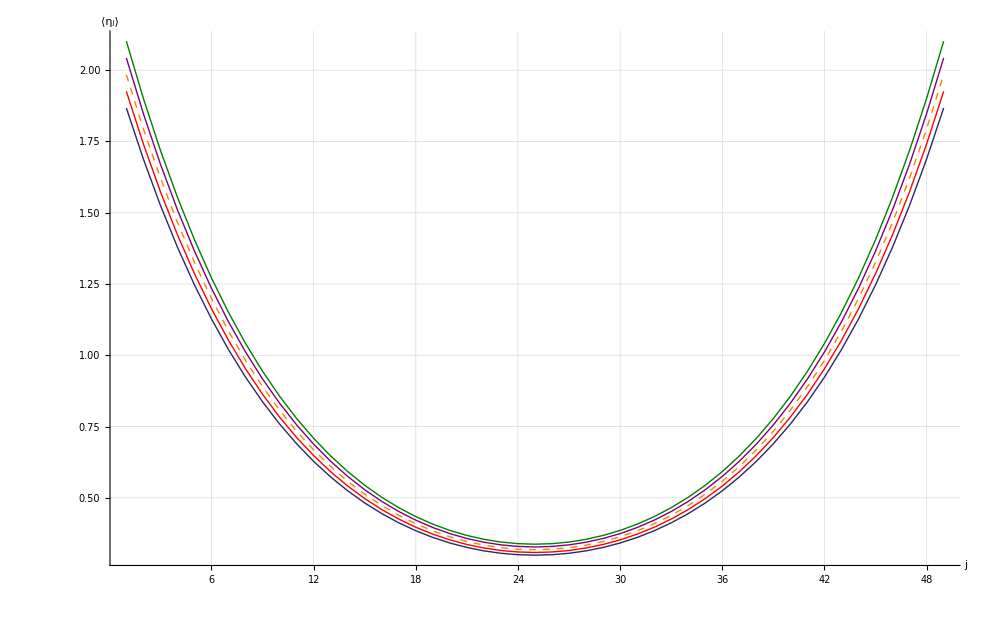

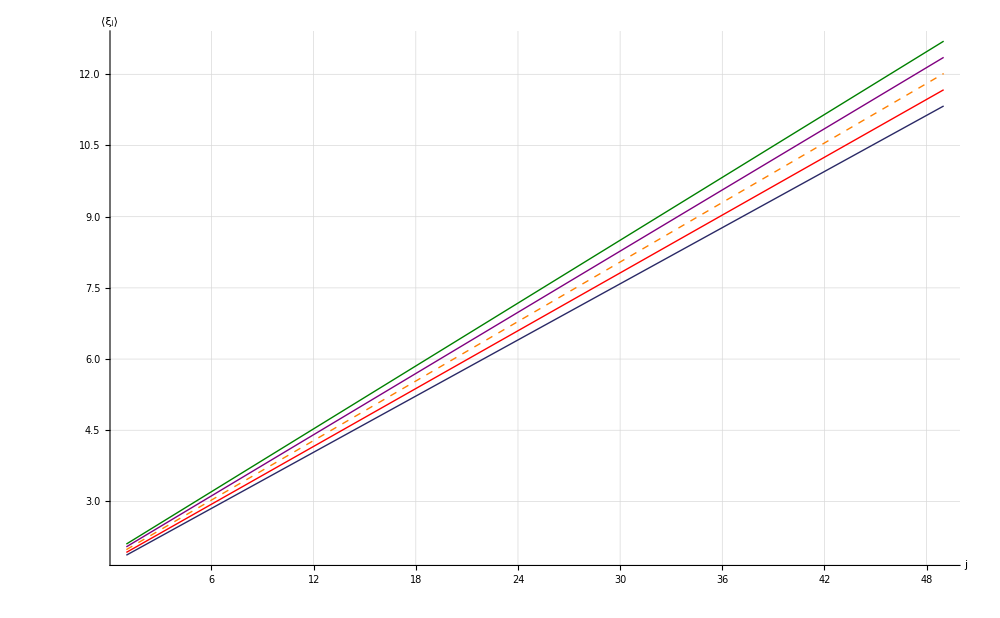

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pIntactMXDη=ListLinePlot[
{
IntactMXDη[[pos1]],
IntactMXDη[[pos2]],
IntactMXDη[[pos3]],
IntactMXDη[[pos4]],
IntactMXDη[[pos5]]
},
ImageSize->1000,
PlotStyle->{
{Thick,Darker[ColorData[1,1]]},
{Thick,Red},
{Thick,Dashed,Orange},
{Thick,Purple},
{Thick,Darker[Green,0.5]}
},
PlotLegend->{
Style["u="<>ToString[(pos1-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos2-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos3-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos4-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos5-1)Δ],FontSize->fs2]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->All,
AxesOrigin->{1,0},
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨η_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.55,
LegendPosition->{0.9,-.2}
]

pIntactMXDξ=ListLinePlot[
{
IntactMXDξ[[pos1]],
IntactMXDξ[[pos2]],
IntactMXDξ[[pos3]],
IntactMXDξ[[pos4]],
IntactMXDξ[[pos5]]
},
ImageSize->1000,
PlotStyle->{
{Thick,Darker[ColorData[1,1]]},
{Thick,Red},
{Thick,Dashed,Orange},
{Thick,Purple},
{Thick,Darker[Green,0.5]}
},
PlotLegend->{
Style["u="<>ToString[(pos1-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos2-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos3-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos4-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos5-1)Δ],FontSize->fs2]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->All,
AxesOrigin->{1,0},
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨ξ_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.55,
LegendPosition->{0.9,-.2}
]
```

### Force-Extension

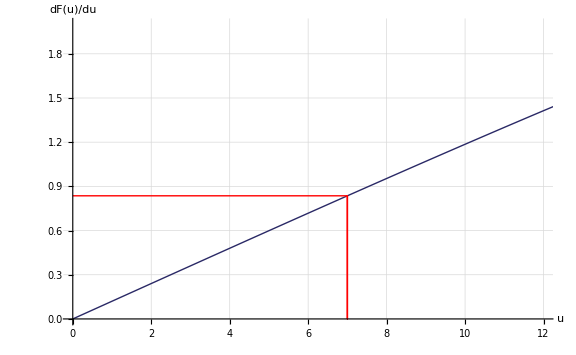

Dimensionless force at (U = 35Δ) = 0.835943

Dimensional Force = 34.049 pN
Dimensional Extension = 7.11828 Å

Dimensional Resultant Average Force = 34.642 pN

```mathematica
fpos={{0,IntactdFE[[upos]][[2]]},{IntactdFE[[upos]][[1]],IntactdFE[[upos]][[2]]},{IntactdFE[[upos]][[1]],0},{IntactdFE[[upos]][[1]],IntactdFE[[upos]][[2]]}};
F=IntactdFE[[upos]][[2]];
u = IntactdFE[[upos]][[1]];

Subscript[resF, c]=(κ (ToDimension[AverageX[[upos]][[n]]-AverageX[[upos]][[n-1]]])+σ (ToDimension[AverageX[[upos]][[n]] -AverageY[[upos]][[n]]]))ToNewton;

pIntactPF=ListLinePlot[
{
IntactdFE,
fpos
},
ImageSize->Large,
PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->{{0,12},{0,2}},
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["dF(u)/du",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
]
Print["Dimensionless force at (U = ",U,"Δ) = ",F]

Subscript[F, c]=ToForceDimension[F];
Print["\nDimensional Force = ",Subscript[F, c] pN,"\nDimensional Extension = ",ToDimension[u]Å,"\n\nDimensional Resultant Average Force = ",Subscript[resF, c] pN,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Subscript[F, c],Subscript[resF, c],NearestValue,κσr}},"Table"];
```

### Average X and Y

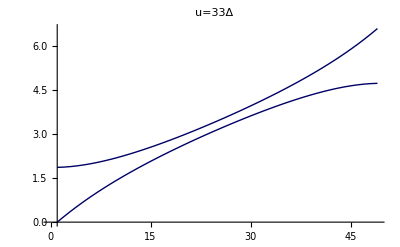
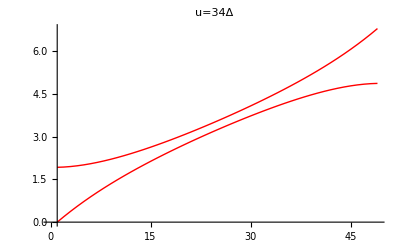
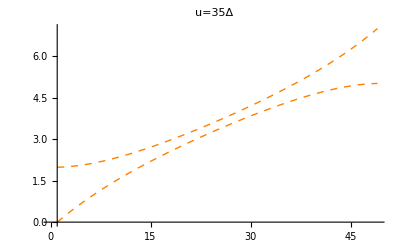
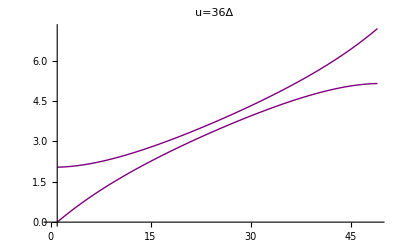
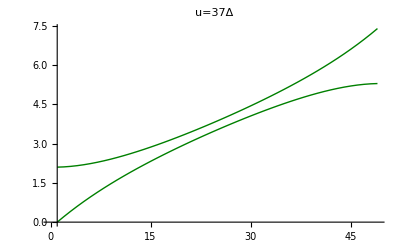

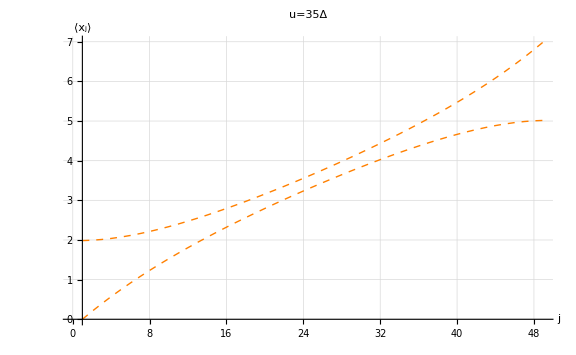

```mathematica
avg1=ListLinePlot[{Chop[AverageX[[pos1]]],Chop[AverageY[[pos1]]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Blue,0.6]}},PlotLabel->"u="<>ToString[pos1-1]<>"Δ"];
avg2=ListLinePlot[{AverageX[[pos2]],AverageY[[pos2]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Red}},PlotLabel->"u="<>ToString[pos2-1]<>"Δ"];
avg3=ListLinePlot[{AverageX[[pos3]],AverageY[[pos3]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Dashed,Orange}},PlotLabel->"u="<>ToString[pos3-1]<>"Δ"];
avg4=ListLinePlot[{AverageX[[pos4]],AverageY[[pos4]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Purple}},PlotLabel->"u="<>ToString[pos4-1]<>"Δ"];
avg5=ListLinePlot[{AverageX[[pos5]],AverageY[[pos5]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Green,0.5]}},PlotLabel->"u="<>ToString[pos5-1]<>"Δ"];
{avg1,avg2,avg3,avg4,avg5}
Show[avg3,ImageSize->Large,GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨x_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}]
```

64

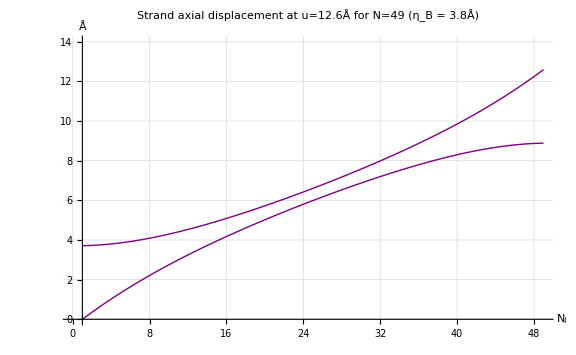

```mathematica
pos4=64
avg4=ListLinePlot[{AverageX[[pos4]],AverageY[[pos4]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Purple}},PlotLabel->Style["Strand axial displacement at u="<>ToString[(pos4-1)Δ]<>"Å for N=49\n (η_B = 3.8Å)",FontSize->fsTitle]];
Show[{avg4},
PlotRange->{{0,49},{0,14}},
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{
Style["N_j",FontSize->fsAxesLabel],
Style["Å",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}]
```